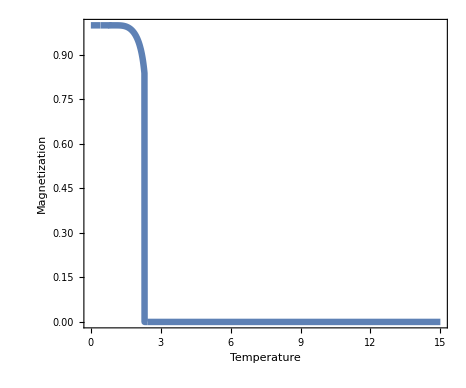

```mathematica
Plot[Sqrt[Piecewise[{{1, v<0.8},{(1-((1-v^2)/(2v))^4)^(1/4), 0.8<v&&v<2.3}}, 0]], {v, 0, 15}, PerformanceGoal->"Quality",PlotStyle->{Thickness[0.01]}, 
FrameLabel->(Style[#,Black,24,Bold]&/@{"Temperature","Magnetization"}),
FrameStyle->Directive[Bold,Black, Thick], Frame->True, AspectRatio->1/1.2]
```